```mathematica
allCrit=Map[Sort,BooleanMinimize[Reduce[
With[
{base="C",colofour="colofour"},
Fold[And,
Map[Fold[Or,Table[var>(var/.RepAtLeast[base]),{var,ListofVars[(allGraphs5[#,colofour]/.RepZero[base])]}]]&,
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
]
]
]
]]]
```

1
 |  |  |  |

```mathematica
BaseCoeff2[formula_,base_]:=Table[Coefficient[formula,var],{var,Bases[base,"Variables"]}]
```

```mathematica
ExpressionToList[exp_]:=Table[exp[[k]],{k,Length[exp]}]
```

```mathematica
matCrit=Map[BaseCoeff2[Total[ListofVars[#]],"C"]&,Select[ExpressionToList[allCrit],Length[#]==15&]];
```

```mathematica
MatrixForm[Take[matCrit,{29,32}],TableHeadings->{None, Map[Rotate[SymbolToLabel2[#],Pi/2]&,Bases["C","Variables"]]}]
```

(OverHat[1] | 12 | 13 | 14 | 15 | 23 | 24 | 25 | 34 | 35 | 45 | 123 | 124 | 125 | 12♁34 | 12♁35 | 12♁45 | 134 | 135 | 13♁24 | 13♁25 | 13♁45 | 145 | 14♁23 | 14♁25 | 14♁35 | 15♁23 | 15♁24 | 15♁34 | 234 | 235 | 23♁45 | 245 | 24♁35 | 25♁34 | 345 | 1234 | 1235 | 123♁45 | 1245 | 124♁35 | 125♁34 | 12♁345 | 1345 | 134♁25 | 135♁24 | 13♁245 | 145♁23 | 14♁235 | 15♁234 | 2345 | OverHat[0]
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MemberQ[matCrit,matCrit[[1]]]
```

Part::partw: Part 1 of {} does not exist.

False

```mathematica
MatrixRank[matCrit]
```

MatrixRank::matrix: Argument {} at position 1 is not a non-empty rectangular matrix.

MatrixRank[{}]

```mathematica
vectorToSymbols[vector_]:=Total [With[{syms=Bases["C","Variables"]},
Table[vector[[i]]syms[[i]],{i,Length[vector]}]
]]
```

```mathematica
(Map[vectorToSymbols,matCrit//LatticeReduce]//TableForm)/.RepGraph["C"]
```

-Graphics-368980+-Graphics-368170+-Graphics-303340+-Graphics-302530
-Graphics-319840+-Graphics-319540+-Graphics-297970+-Graphics-297670
-Graphics-383080+-Graphics-382810+-Graphics-295600+-Graphics-295330
-Graphics-361940+-Graphics-360860+-Graphics-296330+-Graphics-295250
-Graphics-514780+-Graphics-514750+-Graphics-492100+-Graphics-492070
-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270
-Graphics-514780+-Graphics-382810+-Graphics-319540+-Graphics-361660+-Graphics-368170+-Graphics-297970+-Graphics-361120+-Graphics-360860+-Graphics-303340+-Graphics-296330+-Graphics-317380+-Graphics-295600+-Graphics-317140+-Graphics-296080+-Graphics-492070

```mathematica
Select[Keys[allGraphs5],MemberQ[matCrit,BaseCoeff2[allGraphs5[#,"colofour"]]]&]
```

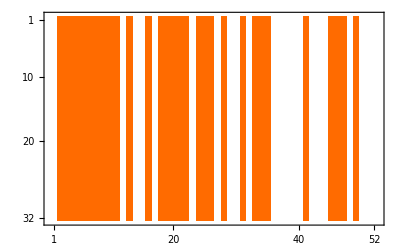

```mathematica
MatrixPlot[Take[matCrit,32]+Reverse[Take[matCrit,{33,64}]]]
```

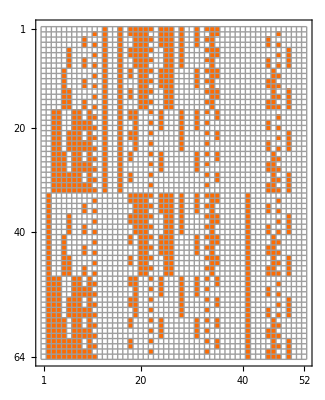

```mathematica
MatrixPlot[matCrit//Sort,Mesh->True,FrameTicks->{{All,All},{All,Flatten[With[{all=Bases["C","Variables"]},Table[Position[all,allGraphs5[k,"colofour"]],{k,alfa1s}]]]}},
FrameTicksStyle->{{Blue,Blue},{Blue,Blue}}]
```

```mathematica
Table[ShowGraph5Least[k],{k,ListofVars[allCrit[[1]]]/.RepKey["C"]}]
```

{-Graphics-514780,-Graphics-492070,-Graphics-383080,-Graphics-368980,-Graphics-361940,-Graphics-361660,-Graphics-361120,-Graphics-319840,-Graphics-317380,-Graphics-317140,-Graphics-302530,-Graphics-297670,-Graphics-296080,-Graphics-295330,-Graphics-295250}

```mathematica
Table[allGraphs5[k,"comp"]=Greater;allGraphs5[k,"compwhy"]=ToString[allCrit[[1]]];
allGraphs5[k,"atleast"]=1;allGraphs5[k,"atleastwhy"]=ToString[allCrit[[1]]];k,{k,ListofVars[allCrit[[1]]]/.RepKey["C"]}]
```

{51478,49207,38308,36898,36194,36166,36112,31984,31738,31714,30253,29767,29608,29533,29525}

```mathematica
Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Table[ShowGraph5Least[k],{k,ListofVars[allCrit[[1]]]/.RepKey["C"]}]
```

{-Graphics-514781,-Graphics-492071,-Graphics-383081,-Graphics-368981,-Graphics-361941,-Graphics-361661,-Graphics-361121,-Graphics-319841,-Graphics-317381,-Graphics-317141,-Graphics-302531,-Graphics-297671,-Graphics-296081,-Graphics-295331,-Graphics-295251}

```mathematica
PropagateComp[]:=Block[{leftKey,rightKey,left,right,current,changed=0},
Monitor[
Table[
current = allGraphs5[k];
Table[
leftKey=children[[1]];
rightKey=children[[2]];
left=allGraphs5[leftKey];
right=allGraphs5[rightKey];
If[current["comp"]===GreaterEqual && (left["comp"]===Greater),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (greater propagated from left)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===GreaterEqual && (right["comp"]===Greater),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (greater propagated from right)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===GreaterEqual && (left["comp"]===Equal&&right["comp"]===Equal),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (zero propagated)";
current["comp"]=Equal;
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];
If[current["comp"]===GreaterEqual && (left["comp"]===Equal&&right["comp"]===Greater),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (Greater (right) and zero (left) propagated)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===GreaterEqual && (left["comp"]===Greater&&right["comp"]===Equal),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (Zero (right) and Greater (left) propagated)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===Greater && (left["comp"]===GreaterEqual&&right["comp"]===Equal),
left["compwhy"]="The down relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (Greater(parent) and zero(right) pushed down to left)";
left["comp"]=Greater;
Print[left["compwhy"]];
changed++;
allGraphs5[children[[1]]]=left;
];

If[current["comp"]===Greater && (left["comp"]===Equal&&right["comp"]===GreaterEqual),
right["compwhy"]="The down relation holds "<> ToString[k]<> "("<> ToString[current["comp"]]<> ") == "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> " (" <>ToString[right["comp"]]<>") (Greater(parent) and zero(left) pushed down to right)";
right["comp"]=Greater;
Print[right["compwhy"]];
changed++;
allGraphs5[children[[2]]]=right;
]
,{children,allGraphs5[k,"children"]}
]
,
{k,Keys[allGraphs5]}],
k
];
changed
]
```

```mathematica
PropagateComp[]
```

The relation holds 29520(GreaterEqual)== 29521(GreaterEqual) + 29525 (Greater) (greater propagated from right)

The relation holds 29523(GreaterEqual)== 29524(Equal) + 29525 (Greater) (greater propagated from right)

The relation holds 29514(GreaterEqual)== 29523(Greater) + 29533 (Greater) (greater propagated from left)

The relation holds 29515(GreaterEqual)== 29524(Equal) + 29533 (Greater) (greater propagated from right)

The relation holds 29512(GreaterEqual)== 29521(GreaterEqual) + 29533 (Greater) (greater propagated from right)

The relation holds 29493(GreaterEqual)== 29520(Greater) + 29551 (GreaterEqual) (greater propagated from left)

The relation holds 29496(GreaterEqual)== 29523(Greater) + 29551 (GreaterEqual) (greater propagated from left)

The relation holds 29574(GreaterEqual)== 29577(GreaterEqual) + 29608 (Greater) (greater propagated from right)

The relation holds 29602(GreaterEqual)== 29605(GreaterEqual) + 29608 (Greater) (greater propagated from right)

The relation holds 29439(GreaterEqual)== 29520(Greater) + 29602 (Greater) (greater propagated from left)

The relation holds 29442(GreaterEqual)== 29523(Greater) + 29605 (GreaterEqual) (greater propagated from left)

The relation holds 29446(GreaterEqual)== 29527(GreaterEqual) + 29608 (Greater) (greater propagated from right)

The relation holds 29440(GreaterEqual)== 29521(GreaterEqual) + 29602 (Greater) (greater propagated from right)

The relation holds 29433(GreaterEqual)== 29514(Greater) + 29605 (GreaterEqual) (greater propagated from left)

The relation holds 29434(GreaterEqual)== 29515(Greater) + 29605 (GreaterEqual) (greater propagated from left)

The relation holds 29431(GreaterEqual)== 29512(Greater) + 29602 (Greater) (greater propagated from left)

The relation holds 29281(GreaterEqual)== 29524(Equal) + 29767 (Greater) (greater propagated from right)

The relation holds 29278(GreaterEqual)== 29521(GreaterEqual) + 29767 (Greater) (greater propagated from right)

The relation holds 29272(GreaterEqual)== 29515(Greater) + 29767 (Greater) (greater propagated from left)

The relation holds 29269(GreaterEqual)== 29512(Greater) + 29767 (Greater) (greater propagated from left)

The relation holds 29254(GreaterEqual)== 29497(GreaterEqual) + 29767 (Greater) (greater propagated from right)

The relation holds 29200(GreaterEqual)== 29443(GreaterEqual) + 29767 (Greater) (greater propagated from right)

The relation holds 29197(GreaterEqual)== 29440(Greater) + 29767 (Greater) (greater propagated from left)

The relation holds 29173(GreaterEqual)== 29416(GreaterEqual) + 29767 (Greater) (greater propagated from right)

The relation holds 29176(GreaterEqual)== 29446(Greater) + 29797 (GreaterEqual) (greater propagated from left)

The relation holds 28791(GreaterEqual)== 29520(Greater) + 30253 (Greater) (greater propagated from left)

The relation holds 28794(GreaterEqual)== 29523(Greater) + 30253 (Greater) (greater propagated from left)

The relation holds 28795(GreaterEqual)== 29524(Equal) + 30253 (Greater) (greater propagated from right)

The relation holds 28792(GreaterEqual)== 29521(GreaterEqual) + 30253 (Greater) (greater propagated from right)

The relation holds 28764(GreaterEqual)== 29493(Greater) + 30253 (Greater) (greater propagated from left)

The relation holds 28767(GreaterEqual)== 29496(Greater) + 30253 (Greater) (greater propagated from left)

The relation holds 28768(GreaterEqual)== 29497(GreaterEqual) + 30253 (Greater) (greater propagated from right)

The relation holds 28765(GreaterEqual)== 29494(GreaterEqual) + 30253 (Greater) (greater propagated from right)

The relation holds 28845(GreaterEqual)== 29574(Greater) + 30334 (GreaterEqual) (greater propagated from left)

The relation holds 28873(GreaterEqual)== 29602(Greater) + 30334 (GreaterEqual) (greater propagated from left)

The relation holds 31708(GreaterEqual)== 31711(GreaterEqual) + 31714 (Greater) (greater propagated from right)

The relation holds 31684(GreaterEqual)== 31711(GreaterEqual) + 31738 (Greater) (greater propagated from right)

The relation holds 31465(GreaterEqual)== 31708(Greater) + 31954 (GreaterEqual) (greater propagated from left)

The relation holds 31492(GreaterEqual)== 31738(Greater) + 31984 (Greater) (greater propagated from left)

The relation holds 31441(GreaterEqual)== 31684(Greater) + 31954 (GreaterEqual) (greater propagated from left)

The relation holds 31444(GreaterEqual)== 31714(Greater) + 31984 (Greater) (greater propagated from left)

The relation holds 27333(GreaterEqual)== 29520(Greater) + 31708 (Greater) (greater propagated from left)

The relation holds 27336(GreaterEqual)== 29523(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27340(GreaterEqual)== 29527(GreaterEqual) + 31714 (Greater) (greater propagated from right)

The relation holds 27334(GreaterEqual)== 29521(GreaterEqual) + 31708 (Greater) (greater propagated from right)

The relation holds 27327(GreaterEqual)== 29514(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27328(GreaterEqual)== 29515(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27325(GreaterEqual)== 29512(Greater) + 31708 (Greater) (greater propagated from left)

The relation holds 27355(GreaterEqual)== 29542(GreaterEqual) + 31738 (Greater) (greater propagated from right)

The relation holds 27364(GreaterEqual)== 29551(GreaterEqual) + 31738 (Greater) (greater propagated from right)

The relation holds 27309(GreaterEqual)== 29496(Greater) + 31684 (Greater) (greater propagated from left)

The relation holds 27310(GreaterEqual)== 29497(GreaterEqual) + 31684 (Greater) (greater propagated from right)

The relation holds 27255(GreaterEqual)== 29442(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27246(GreaterEqual)== 29433(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27247(GreaterEqual)== 29434(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27273(GreaterEqual)== 29460(GreaterEqual) + 31738 (Greater) (greater propagated from right)

The relation holds 27282(GreaterEqual)== 29469(GreaterEqual) + 31738 (Greater) (greater propagated from right)

The relation holds 26608(GreaterEqual)== 28795(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 26605(GreaterEqual)== 28792(Greater) + 31708 (Greater) (greater propagated from left)

The relation holds 26581(GreaterEqual)== 28768(Greater) + 31684 (Greater) (greater propagated from left)

The relation holds 36057(GreaterEqual)== 36084(GreaterEqual) + 36112 (Greater) (greater propagated from right)

The relation holds 36058(GreaterEqual)== 36085(GreaterEqual) + 36112 (Greater) (greater propagated from right)

The relation holds 36138(GreaterEqual)== 36166(Greater) + 36194 (Greater) (greater propagated from left)

The relation holds 36003(GreaterEqual)== 36084(GreaterEqual) + 36166 (Greater) (greater propagated from right)

The relation holds 36004(GreaterEqual)== 36085(GreaterEqual) + 36166 (Greater) (greater propagated from right)

The relation holds 36030(GreaterEqual)== 36112(Greater) + 36194 (Greater) (greater propagated from left)

The relation holds 35325(GreaterEqual)== 36057(Greater) + 36817 (GreaterEqual) (greater propagated from left)

The relation holds 35326(GreaterEqual)== 36058(Greater) + 36817 (GreaterEqual) (greater propagated from left)

The relation holds 35406(GreaterEqual)== 36138(Greater) + 36898 (Greater) (greater propagated from left)

The relation holds 35434(GreaterEqual)== 36166(Greater) + 36898 (Greater) (greater propagated from left)

The relation holds 33916(GreaterEqual)== 36112(Greater) + 38308 (Greater) (greater propagated from left)

The relation holds 33807(GreaterEqual)== 36003(Greater) + 38281 (GreaterEqual) (greater propagated from left)

The relation holds 33808(GreaterEqual)== 36004(Greater) + 38281 (GreaterEqual) (greater propagated from left)

The relation holds 33834(GreaterEqual)== 36030(Greater) + 38308 (Greater) (greater propagated from left)

The relation holds 22954(GreaterEqual)== 29515(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22951(GreaterEqual)== 29512(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22981(GreaterEqual)== 29542(GreaterEqual) + 36112 (Greater) (greater propagated from right)

The relation holds 22990(GreaterEqual)== 29551(GreaterEqual) + 36112 (Greater) (greater propagated from right)

The relation holds 22936(GreaterEqual)== 29497(GreaterEqual) + 36058 (Greater) (greater propagated from right)

The relation holds 23044(GreaterEqual)== 29605(GreaterEqual) + 36166 (Greater) (greater propagated from right)

The relation holds 22882(GreaterEqual)== 29443(GreaterEqual) + 36004 (Greater) (greater propagated from right)

The relation holds 22873(GreaterEqual)== 29434(Greater) + 36004 (Greater) (greater propagated from left)

The relation holds 22720(GreaterEqual)== 29281(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22717(GreaterEqual)== 29278(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22711(GreaterEqual)== 29272(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22708(GreaterEqual)== 29269(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22735(GreaterEqual)== 29296(GreaterEqual) + 36112 (Greater) (greater propagated from right)

The relation holds 22744(GreaterEqual)== 29305(GreaterEqual) + 36112 (Greater) (greater propagated from right)

The relation holds 22693(GreaterEqual)== 29254(Greater) + 36058 (Greater) (greater propagated from left)

The relation holds 22639(GreaterEqual)== 29200(Greater) + 36004 (Greater) (greater propagated from left)

The relation holds 22234(GreaterEqual)== 28795(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22207(GreaterEqual)== 28768(Greater) + 36058 (Greater) (greater propagated from left)

The relation holds 22315(GreaterEqual)== 28876(GreaterEqual) + 36166 (Greater) (greater propagated from right)

The relation holds 22318(GreaterEqual)== 29608(Greater) + 36898 (Greater) (greater propagated from left)

The relation holds 25138(GreaterEqual)== 31708(Greater) + 38281 (GreaterEqual) (greater propagated from left)

The relation holds 25168(GreaterEqual)== 31738(Greater) + 38308 (Greater) (greater propagated from left)

The relation holds 24895(GreaterEqual)== 31465(Greater) + 38281 (GreaterEqual) (greater propagated from left)

The relation holds 24922(GreaterEqual)== 31492(Greater) + 38308 (Greater) (greater propagated from left)

The relation holds 20047(GreaterEqual)== 26608(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 20050(GreaterEqual)== 27340(Greater) + 36817 (GreaterEqual) (greater propagated from left)

The relation holds 9841(GreaterEqual)== 29524(Equal) + 49207 (Greater) (greater propagated from right)

The relation holds 9814(GreaterEqual)== 29497(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 9760(GreaterEqual)== 29443(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 9763(GreaterEqual)== 29446(Greater) + 49210 (GreaterEqual) (greater propagated from left)

The relation holds 9733(GreaterEqual)== 29416(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 9598(GreaterEqual)== 29281(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 9571(GreaterEqual)== 29254(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 9517(GreaterEqual)== 29200(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 9490(GreaterEqual)== 29173(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 9493(GreaterEqual)== 29176(Greater) + 49210 (GreaterEqual) (greater propagated from left)

The relation holds 9112(GreaterEqual)== 28795(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 11950(GreaterEqual)== 31714(Greater) + 51478 (Greater) (greater propagated from left)

The relation holds 11920(GreaterEqual)== 31684(Greater) + 51475 (GreaterEqual) (greater propagated from left)

The relation holds 11677(GreaterEqual)== 31441(Greater) + 51475 (GreaterEqual) (greater propagated from left)

The relation holds 11680(GreaterEqual)== 31444(Greater) + 51478 (Greater) (greater propagated from left)

The relation holds 7654(GreaterEqual)== 27337(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 7657(GreaterEqual)== 27340(Greater) + 49210 (GreaterEqual) (greater propagated from left)

The relation holds 7627(GreaterEqual)== 27310(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 7738(GreaterEqual)== 29608(Greater) + 51478 (Greater) (greater propagated from left)

The relation holds 6925(GreaterEqual)== 26608(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 3280(GreaterEqual)== 22963(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 3253(GreaterEqual)== 22936(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 3199(GreaterEqual)== 22882(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 2551(GreaterEqual)== 22234(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 1093(GreaterEqual)== 20776(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 1174(GreaterEqual)== 23044(Greater) + 51475 (GreaterEqual) (greater propagated from left)

The relation holds 364(GreaterEqual)== 20047(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 367(GreaterEqual)== 20050(Greater) + 49210 (GreaterEqual) (greater propagated from left)

The relation holds 445(GreaterEqual)== 22315(Greater) + 51475 (GreaterEqual) (greater propagated from left)

The relation holds 448(GreaterEqual)== 22318(Greater) + 51478 (Greater) (greater propagated from left)

130

```mathematica
PropagateComp[]
```

0

```mathematica
PropagateAtLeast2[]:=Block[{newValue,current,left,right,changes=0,result={}},
Table[
Table[
current=allGraphs5[k];
left=allGraphs5[c[[1]]];
right=allGraphs5[c[[2]]];

If[left["comp"]===Equal && right["comp"]=!=Equal &&current["atleast"]≠right["atleast"],
allGraphs5[k,"atleastwhy"]="Propagate from relation " <> ToString[c] <>" with values " <> ToString[{left["atleast"],right["atleast"]}]<>" and comp " <> ToString[{left["comp"],right["comp"]}]<>" (from right)";
allGraphs5[k,"atleast"]=Max[current["atleast"],left["atleast"]+right["atleast"]];
Print[allGraphs5[k,"atleastwhy"]];
allGraphs5[k,"atleast"]=right["atleast"];
changes++
];

If[right["comp"]===Equal && left["comp"]=!=Equal &&current["atleast"]≠left["atleast"],
allGraphs5[k,"atleastwhy"]="Propagate from relation " <> ToString[c] <>" with values " <> ToString[{left["atleast"],right["atleast"]}]<>" and comp " <> ToString[{left["comp"],right["comp"]}]<>" (from left)";
allGraphs5[k,"atleast"]=Max[current["atleast"],left["atleast"]+right["atleast"]];
Print[allGraphs5[k,"atleastwhy"]];
allGraphs5[k,"atleast"]=left["atleast"];
changes++
];

If[current["comp"]===Greater &&  right["comp"]===Equal &&current["atleast"]>left["atleast"],
allGraphs5[c[[1]],"atleastwhy"]="Propagate from relation " <> ToString[c] <>" with values " <> ToString[{left["atleast"],right["atleast"]}]<>" and comp " <> ToString[{left["comp"],right["comp"]}]<>" (from parent to left)";
allGraphs5[c[[1]],"atleast"]=current["atleast"];
Print[allGraphs5[c[[1]],"atleastwhy"]];
changes++
];

If[current["comp"]===Greater && left["comp"]===Equal  &&current["atleast"]>right["atleast"],
allGraphs5[c[[2]],"atleastwhy"]="Propagate from relation " <> ToString[c] <>" with values " <> ToString[{left["atleast"],right["atleast"]}]<>" and comp " <> ToString[{left["comp"],right["comp"]}]<>" (from parent to right)";
allGraphs5[c[[2]],"atleast"]=current["atleast"];
Print[allGraphs5[c[[2]],"atleastwhy"]];
changes++
];
,{c,allGraphs5[k,"children"]}
]
,{k,Keys[allGraphs5]}
];
{changes,result}
]
```

```mathematica
ShowGraph5Least[29525]
```

-Graphics-295251

```mathematica
PropagateAtLeast2[]
```

Propagate from relation {29524, 29525} with values {0, 1} and comp {Equal, Greater} (from right)

Propagate from relation {29524, 29533} with values {0, 1} and comp {Equal, Greater} (from right)

Propagate from relation {29524, 29767} with values {0, 1} and comp {Equal, Greater} (from right)

Propagate from relation {29524, 30253} with values {0, 1} and comp {Equal, Greater} (from right)

Propagate from relation {29524, 49207} with values {0, 1} and comp {Equal, Greater} (from right)

{5,{}}

```mathematica
PropagateAtLeast2[]
```

{0,{}}

```mathematica
allCrit2=With[
{base="C",colofour="colofour"},
Fold[And,
Map[Fold[Or,Table[var>(var/.RepAtLeast[base]),{var,ListofVars[(allGraphs5[#,colofour]/.RepZero[base])]}]]&,
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
]
]
]
```

1
 |  |  |  |

```mathematica
Length[allCrit2]
```

1163

```mathematica
allCrit2=Reduce[allCrit2]
```

(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x35>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x23x45>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v1245x3>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x345>1&&v1235x4>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x2x34>1&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x234x5>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v1245x3>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x345>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v13x2x4x5>0&&v13x245>1&&v14x235>1&&v135x24>1&&v14x2x35>1&&v134x25>1&&v14x2x3x5>0&&v12x3x45>1&&v15x2x3x4>1&&v12x34x5>1&&v1x23x4x5>1&&v125x3x4>1&&v1x24x35>1&&v1245x3>1&&v1x24x3x5>0&&v123x4x5>1&&v1x25x3x4>0&&v1235x4>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v1245x3>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v1245x3>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x345>1&&v1235x4>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v1245x3>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x35>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v12x3x45>1&&v1x23x45>1&&v12x34x5>1&&v1x23x4x5>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x345>1&&v1235x4>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x2x34>1&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v12x3x45>1&&v1x234x5>1&&v12x34x5>1&&v1x23x4x5>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x345>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v13x2x4x5>0&&v14x25x3>1&&v13x245>1&&v14x2x35>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v12x3x45>1&&v1x2345>1&&v12x34x5>1&&v1x23x4x5>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v12x3x4x5>1&&v1x23x45>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v12x3x4x5>1&&v1x23x45>1&&v12x3x45>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x345>1&&v1235x4>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v145x2x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x345>1&&v1235x4>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x345>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v13x2x4x5>0&&v14x25x3>1&&v13x245>1&&v14x2x35>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v123x4x5>1&&v1x25x3x4>0&&v1235x4>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x345>1&&v1235x4>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v15x23x4>1&&v14x25x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v1235x4>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v1245x3>1&&v1x25x3x4>0&&v1235x4>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v12x3x4x5>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1235x4>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x3x5>0&&v14x2x35>1&&v15x2x34>1&&v14x25x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v145x2x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v1235x4>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v1235x4>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x35>1&&v13x25x4>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v13x2x4x5>0&&v13x25x4>1&&v14x235>1&&v13x245>1&&v14x2x35>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v1245x3>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x25x4>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v1345x2>1&&v1x23x45>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x25x4>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x45>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v1345x2>1&&v1x234x5>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x25x3>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v1345x2>1&&v1x2345>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x25x3>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v145x2x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x45>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v13x2x4x5>0&&v14x2x35>1&&v13x25x4>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v1345x2>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v1345x2>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v15x23x4>1&&v14x25x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x25x4>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v13x2x4x5>0&&v14x2x35>1&&v13x25x4>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x23x4>1&&v145x2x3>1&&v15x2x34>1&&v13x2x4x5>0&&v1x234x5>1&&v13x25x4>1&&v1x23x45>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x23x4>1&&v145x2x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x25x4>1&&v1x23x45>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v15x23x4>1&&v14x2x35>1&&v15x2x3x4>1&&v14x25x3>1&&v1x234x5>1&&v13x2x4x5>0&&v1x23x45>1&&v13x25x4>1&&v1x24x35>1&&v13x245>1&&v1x24x3x5>0&&v135x24>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v145x2x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x25x4>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x23x4>1&&v145x2x3>1&&v15x2x34>1&&v13x2x4x5>0&&v1x234x5>1&&v13x25x4>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x23x4>1&&v145x2x3>1&&v15x2x34>1&&v13x2x4x5>0&&v1x23x4x5>1&&v13x25x4>1&&v1x24x35>1&&v13x245>1&&v1x24x3x5>0&&v135x24>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x3x5>0&&v14x2x35>1&&v15x2x34>1&&v14x25x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x25x4>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x2x3x4>1&&v145x2x3>1&&v1x23x45>1&&v13x2x4x5>0&&v1x23x4x5>1&&v13x25x4>1&&v1x24x35>1&&v13x245>1&&v1x24x3x5>0&&v135x24>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x35x4>0&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x2x34x5>1&&v1234x5>1&&v1x2x3x45>1&&v12345>1)||(v13x2x4x5>0&&v145x2x3>1&&v13x24x5>1&&v14x235>1&&v13x245>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v1345x2>1&&v1x23x45>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v12345>1)||(v13x2x4x5>0&&v14x235>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x34>1&&v134x25>1&&v15x2x3x4>1&&v1345x2>1&&v1x234x5>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v13x24x5>1&&v13x2x4x5>0&&v13x245>1&&v14x235>1&&v134x25>1&&v14x2x3x5>0&&v1345x2>1&&v15x2x3x4>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x23x4>1&&v13x245>1&&v15x2x3x4>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v145x2x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v13x2x4x5>0&&v14x235>1&&v13x24x5>1&&v14x2x35>1&&v13x245>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v1245x3>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v12345>1)||(v14x2x3x5>0&&v14x2x35>1&&v15x23x4>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v13x2x4x5>0&&v14x235>1&&v13x24x5>1&&v14x25x3>1&&v13x245>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x35>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x45>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v13x2x4x5>0&&v14x25x3>1&&v13x24x5>1&&v14x2x35>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v12345>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v13x2x4x5>0&&v14x2x35>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x23x4>1&&v145x2x3>1&&v15x2x34>1&&v13x2x4x5>0&&v1x234x5>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x23x4>1&&v145x2x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v12345>1)||(v15x23x4>1&&v14x2x35>1&&v15x2x3x4>1&&v14x25x3>1&&v1x234x5>1&&v13x2x4x5>0&&v1x23x45>1&&v13x24x5>1&&v1x24x35>1&&v13x245>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v13x2x4x5>0&&v14x235>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x23x4>1&&v134x25>1&&v15x2x34>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x35>1&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v12345>1)||(v13x2x4x5>0&&v14x235>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x2x3x5>0&&v14x2x35>1&&v15x2x34>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x23x45>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v145x2x3>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x23x4>1&&v145x2x3>1&&v15x2x34>1&&v13x2x4x5>0&&v1x234x5>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x2x3x5>0&&v15x2x34>1&&v14x2x35>1&&v15x2x3x4>1&&v14x25x3>1&&v1x234x5>1&&v13x2x4x5>0&&v1x23x4x5>1&&v13x24x5>1&&v1x24x35>1&&v13x245>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x2x3x4>1&&v145x2x3>1&&v1x23x45>1&&v13x2x4x5>0&&v1x23x4x5>1&&v13x24x5>1&&v1x24x35>1&&v13x245>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x3x45>1&&v12345>1)||(v13x2x4x5>0&&v145x2x3>1&&v13x25x4>1&&v14x235>1&&v13x24x5>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v1345x2>1&&v1x23x45>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x2x34>1&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v1345x2>1&&v1x234x5>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v13x25x4>1&&v13x2x4x5>0&&v13x24x5>1&&v14x235>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v1345x2>1&&v1x2345>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v15x2x3x4>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v13x2x4x5>0&&v13x25x4>1&&v14x235>1&&v13x24x5>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x35>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x45>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x2x35>1&&v13x24x5>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x24x5>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x23x45>1&&v13x24x5>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v13x2x4x5>0&&v14x2x35>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v145x2x3>1&&v15x2x34>1&&v13x2x4x5>0&&v1x234x5>1&&v13x25x4>1&&v1x23x45>1&&v13x24x5>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v145x2x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x25x4>1&&v1x23x45>1&&v13x24x5>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v14x2x3x5>0&&v15x23x4>1&&v14x2x35>1&&v15x2x3x4>1&&v14x235>1&&v1x234x5>1&&v13x2x4x5>0&&v1x23x45>1&&v13x25x4>1&&v1x24x35>1&&v13x24x5>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v145x2x3>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v135x24>1&&v1x23x45>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x23x45>1&&v13x24x5>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v145x2x3>1&&v15x2x34>1&&v13x2x4x5>0&&v1x234x5>1&&v13x25x4>1&&v1x23x45>1&&v13x24x5>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x23x4>1&&v145x2x3>1&&v15x2x34>1&&v13x2x4x5>0&&v1x2345>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x45>1&&v135x24>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v145x2x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x25x4>1&&v1x23x45>1&&v13x24x5>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x23x4>1&&v145x2x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x45>1&&v135x24>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v14x2x3x5>0&&v14x25x3>1&&v15x23x4>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x45>1&&v135x24>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x3x5>0&&v15x23x4>1&&v14x25x3>1&&v15x2x3x4>1&&v14x235>1&&v1x234x5>1&&v13x2x4x5>0&&v1x23x45>1&&v13x25x4>1&&v1x24x35>1&&v13x24x5>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v15x23x4>1&&v14x2x35>1&&v15x2x3x4>1&&v14x25x3>1&&v1x2345>1&&v13x2x4x5>0&&v1x234x5>1&&v13x25x4>1&&v1x23x45>1&&v13x24x5>1&&v1x24x3x5>0&&v135x24>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x2x3x4>1&&v145x2x3>1&&v1x23x45>1&&v13x2x4x5>0&&v1x23x4x5>1&&v13x25x4>1&&v1x24x35>1&&v13x24x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v14x2x3x5>0&&v15x2x34>1&&v14x2x35>1&&v15x2x3x4>1&&v14x25x3>1&&v1x234x5>1&&v13x2x4x5>0&&v1x23x4x5>1&&v13x25x4>1&&v1x24x35>1&&v13x24x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x23x4x5>1&&v13x24x5>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x3x5>0&&v15x23x4>1&&v14x2x35>1&&v15x2x34>1&&v14x25x3>1&&v1x234x5>1&&v145x2x3>1&&v1x23x45>1&&v13x2x4x5>0&&v1x24x35>1&&v13x25x4>1&&v1x24x3x5>0&&v13x24x5>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v14x2x3x5>0&&v15x23x4>1&&v14x2x35>1&&v15x2x3x4>1&&v14x25x3>1&&v1x234x5>1&&v145x2x3>1&&v1x23x45>1&&v13x2x4x5>0&&v1x24x35>1&&v13x25x4>1&&v1x24x3x5>0&&v13x24x5>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v12345>1)||(v15x2x3x4>1&&v15x23x4>1&&v1x234x5>1&&v14x2x35>1&&v1x23x45>1&&v14x25x3>1&&v1x24x35>1&&v13x2x4x5>0&&v1x24x3x5>0&&v13x25x4>1&&v1x25x3x4>0&&v13x24x5>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v145x2x3>1&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x2x3x4>1&&v13x25x4>1&&v1x23x45>1&&v13x24x5>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v12345>1)||(v14x235>1&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v14x235>1&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v145x2x3>1&&v15x2x34>1&&v13x2x4x5>0&&v1x234x5>1&&v13x25x4>1&&v1x23x4x5>1&&v13x24x5>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x23x4x5>1&&v13x24x5>1&&v1x24x35>1&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v14x2x3x5>0&&v15x2x34>1&&v14x2x35>1&&v15x2x3x4>1&&v14x235>1&&v1x234x5>1&&v13x2x4x5>0&&v1x23x4x5>1&&v13x25x4>1&&v1x24x35>1&&v13x24x5>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v14x2x3x5>0&&v14x2x35>1&&v15x2x3x4>1&&v14x235>1&&v1x23x45>1&&v145x2x3>1&&v1x23x4x5>1&&v13x25x4>1&&v1x24x35>1&&v13x24x5>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x2x3x4>1&&v13x25x4>1&&v1x23x4x5>1&&v13x24x5>1&&v1x24x35>1&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v145x2x3>1&&v15x2x34>1&&v13x2x4x5>0&&v1x234x5>1&&v13x25x4>1&&v1x23x4x5>1&&v13x24x5>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x23x4>1&&v145x2x3>1&&v15x2x34>1&&v13x2x4x5>0&&v1x2345>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x23x4x5>1&&v13x24x5>1&&v1x24x35>1&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x23x4>1&&v145x2x3>1&&v15x2x34>1&&v13x2x4x5>0&&v1x2345>1&&v13x25x4>1&&v1x23x4x5>1&&v13x24x5>1&&v1x24x3x5>0&&v135x24>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v12345>1)||(v14x2x3x5>0&&v14x25x3>1&&v15x2x34>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x25x4>1&&v1x23x4x5>1&&v13x24x5>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v12345>1)||(v14x2x3x5>0&&v14x2x35>1&&v15x2x34>1&&v14x25x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x3x4>1&&v145x2x3>1&&v1x2345>1&&v13x25x4>1&&v1x23x45>1&&v13x24x5>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v12345>1)||(v14x2x3x5>0&&v14x25x3>1&&v15x2x3x4>1&&v14x235>1&&v1x23x45>1&&v145x2x3>1&&v1x23x4x5>1&&v13x25x4>1&&v1x24x35>1&&v13x24x5>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v12345>1)||(v14x2x3x5>0&&v14x2x35>1&&v15x2x3x4>1&&v14x25x3>1&&v1x2345>1&&v145x2x3>1&&v1x23x45>1&&v13x25x4>1&&v1x23x4x5>1&&v13x24x5>1&&v1x24x3x5>0&&v135x24>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v12345>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v1345x2>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v12345>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x3x4>1&&v13x25x4>1&&v1x23x4x5>1&&v13x24x5>1&&v1x24x35>1&&v1345x2>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v12345>1)||(v14x2x35>1&&v15x2x3x4>1&&v14x25x3>1&&v1x2345>1&&v13x25x4>1&&v1x23x4x5>1&&v13x24x5>1&&v1x24x3x5>0&&v135x24>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v12345>1)||(v14x2x3x5>0&&v15x23x4>1&&v14x2x35>1&&v15x2x34>1&&v14x25x3>1&&v1x234x5>1&&v145x2x3>1&&v1x23x4x5>1&&v13x2x4x5>0&&v1x24x35>1&&v13x25x4>1&&v1x24x3x5>0&&v13x24x5>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v125x3x4>1&&v1x2x3x45>1&&v12345>1)||(v14x2x3x5>0&&v14x2x35>1&&v15x23x4>1&&v14x25x3>1&&v15x2x34>1&&v145x2x3>1&&v1x23x4x5>1&&v13x2x4x5>0&&v1x24x35>1&&v13x25x4>1&&v1x25x3x4>0&&v13x24x5>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v125x3x4>1&&v1x2x3x45>1&&v12345>1)||(v15x2x34>1&&v14x2x3x5>0&&v15x2x3x4>1&&v14x2x35>1&&v1x234x5>1&&v14x25x3>1&&v1x23x4x5>1&&v13x2x4x5>0&&v1x24x35>1&&v13x25x4>1&&v1x24x3x5>0&&v13x24x5>1&&v1x2x345>1&&v12x3x4x5>1&&v1x2x35x4>0&&v12x34x5>1&&v1x2x3x45>1&&v12345>1)||(v15x2x3x4>1&&v14x2x3x5>0&&v1x23x45>1&&v14x2x35>1&&v1x23x4x5>1&&v14x25x3>1&&v1x24x35>1&&v145x2x3>1&&v1x24x3x5>0&&v13x25x4>1&&v1x25x3x4>0&&v13x24x5>1&&v1x2x345>1&&v12x3x4x5>1&&v1x2x34x5>1&&v12x3x45>1&&v1x2x35x4>0&&v12345>1)||(v14x2x35>1&&v15x2x3x4>1&&v14x25x3>1&&v1x23x4x5>1&&v13x25x4>1&&v1x24x35>1&&v13x24x5>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x3x45>1&&v12345>1)||(v13x2x4x5>0&&v145x2x3>1&&v13x245>1&&v14x235>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v1345x2>1&&v1x2345>1&&v12x3x45>1&&v1x23x45>1&&v12x34x5>1&&v1x23x4x5>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v13x2x4x5>0&&v145x2x3>1&&v13x245>1&&v14x235>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v1345x2>1&&v1x23x45>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v13x2x4x5>0&&v14x235>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x34>1&&v134x25>1&&v15x2x3x4>1&&v1345x2>1&&v1x2345>1&&v12x3x45>1&&v1x234x5>1&&v12x34x5>1&&v1x23x4x5>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v13x2x4x5>0&&v14x235>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x34>1&&v134x25>1&&v15x2x3x4>1&&v1345x2>1&&v1x234x5>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v13x245>1&&v13x2x4x5>0&&v135x24>1&&v14x235>1&&v134x25>1&&v14x2x3x5>0&&v1345x2>1&&v15x2x3x4>1&&v12x3x45>1&&v1x2345>1&&v12x34x5>1&&v1x23x4x5>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v13x245>1&&v13x2x4x5>0&&v135x24>1&&v14x235>1&&v134x25>1&&v14x2x3x5>0&&v1345x2>1&&v15x2x3x4>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x35>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v12x3x45>1&&v1x23x45>1&&v12x34x5>1&&v1x23x4x5>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x35>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x23x45>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x2x34>1&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v12x3x45>1&&v1x234x5>1&&v12x34x5>1&&v1x23x4x5>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x2x34>1&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x234x5>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v13x2x4x5>0&&v14x235>1&&v13x245>1&&v14x2x35>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v12x3x45>1&&v1x2345>1&&v12x34x5>1&&v1x23x4x5>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v13x2x4x5>0&&v13x245>1&&v14x235>1&&v135x24>1&&v14x2x35>1&&v134x25>1&&v14x2x3x5>0&&v12x3x45>1&&v15x2x3x4>1&&v12x34x5>1&&v1x23x4x5>1&&v125x3x4>1&&v1x24x35>1&&v124x35>1&&v1x24x3x5>0&&v1245x3>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x23x4>1&&v135x24>1&&v15x2x34>1&&v134x25>1&&v1x2345>1&&v1345x2>1&&v1x234x5>1&&v12x3x4x5>1&&v1x23x45>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x23x4>1&&v135x24>1&&v15x2x34>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v12x3x4x5>1&&v1x23x45>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x23x4>1&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v1345x2>1&&v1x234x5>1&&v12x3x4x5>1&&v1x23x45>1&&v12x3x45>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x23x4>1&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v12x3x4x5>1&&v1x23x45>1&&v12x3x45>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v1345x2>1&&v1x23x45>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x2x34>1&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v1345x2>1&&v1x234x5>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x2x34>1&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v13x2x4x5>0&&v14x235>1&&v13x245>1&&v14x25x3>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v1345x2>1&&v1x2345>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v13x2x4x5>0&&v14x235>1&&v13x245>1&&v14x25x3>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x45>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x35>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x245>1&&v14x2x35>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v123x4x5>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x25x3>1&&v15x23x4>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x25x3>1&&v15x23x4>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x23x4>1&&v135x24>1&&v15x2x34>1&&v134x25>1&&v1x2345>1&&v1345x2>1&&v1x234x5>1&&v12x3x4x5>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x23x4>1&&v135x24>1&&v15x2x34>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v12x3x4x5>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x23x4>1&&v135x24>1&&v15x2x34>1&&v134x25>1&&v1x2345>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x23x4>1&&v135x24>1&&v15x2x34>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x2x34>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x2x34>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x35x4>0&&v1234x5>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1235x4>1&&v1x2x3x45>1&&v1234x5>1)||(v13x2x4x5>0&&v145x2x3>1&&v13x25x4>1&&v14x235>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v1345x2>1&&v1x23x45>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v13x2x4x5>0&&v145x2x3>1&&v13x25x4>1&&v14x235>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x2x3x5>0&&v13x245>1&&v15x2x34>1&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v1345x2>1&&v1x234x5>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x2x3x5>0&&v13x245>1&&v15x2x34>1&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v13x25x4>1&&v13x2x4x5>0&&v13x245>1&&v14x235>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v1345x2>1&&v1x2345>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v13x25x4>1&&v13x2x4x5>0&&v13x245>1&&v14x235>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x35>1&&v13x25x4>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x45>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x35>1&&v13x25x4>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x2x35>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v13x2x4x5>0&&v13x25x4>1&&v14x235>1&&v13x245>1&&v14x2x35>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x25x4>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x25x4>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x25x3>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x25x3>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x35>1&&v13x25x4>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x25x4>1&&v14x2x35>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1234x5>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x25x3>1&&v15x23x4>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x25x4>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x25x3>1&&v15x23x4>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x25x4>1&&v1x23x45>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1234x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x25x4>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x23x45>1&&v13x25x4>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v14x25x3>1&&v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x35>1&&v13x25x4>1&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x3x45>1&&v1234x5>1)||(v13x2x4x5>0&&v145x2x3>1&&v13x24x5>1&&v14x235>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v1345x2>1&&v1x23x45>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v13x2x4x5>0&&v145x2x3>1&&v13x24x5>1&&v14x235>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v13x2x4x5>0&&v14x235>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x34>1&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v1345x2>1&&v1x234x5>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v13x2x4x5>0&&v14x235>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x34>1&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v13x24x5>1&&v13x2x4x5>0&&v13x245>1&&v14x235>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v1345x2>1&&v1x2345>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v13x24x5>1&&v13x2x4x5>0&&v13x245>1&&v14x235>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x35>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x45>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x35>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v13x2x4x5>0&&v14x235>1&&v13x24x5>1&&v14x2x35>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v13x2x4x5>0&&v13x24x5>1&&v14x235>1&&v13x245>1&&v14x2x35>1&&v135x24>1&&v14x2x3x5>0&&v134x25>1&&v15x2x3x4>1&&v12x3x45>1&&v1x23x4x5>1&&v12x34x5>1&&v1x24x35>1&&v125x3x4>1&&v1x24x3x5>0&&v124x35>1&&v1x25x3x4>0&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x23x4>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x23x4>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v124x35>1&&v1x2x345>1&&v1245x3>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v13x2x4x5>0&&v14x235>1&&v13x24x5>1&&v14x25x3>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v13x2x4x5>0&&v14x235>1&&v13x24x5>1&&v14x25x3>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x35>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x24x5>1&&v14x2x35>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v123x4x5>1&&v1x2x35x4>0&&v1235x4>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x2x35>1&&v14x25x3>1&&v15x23x4>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v14x2x35>1&&v14x25x3>1&&v15x23x4>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1&&v1x2x3x45>1&&v1235x4>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v145x2x3>1&&v13x2x4x5>0&&v14x235>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x23x4>1&&v135x24>1&&v15x2x34>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v145x2x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v1235x4>1)||(v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v13x2x4x5>0&&v14x235>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v13x2x4x5>0&&v14x2x35>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x4x5>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v145x2x3>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v14x25x3>1&&v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x2x34>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x25x3>1&&v15x2x34>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x23x45>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1235x4>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v1345x2>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x25x3x4>0&&v1345x2>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x3x5>0&&v135x24>1&&v1x25x3x4>0&&v134x25>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x35>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x3x45>1&&v1235x4>1)||(v13x2x4x5>0&&v145x2x3>1&&v13x25x4>1&&v14x235>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1)||(v13x2x4x5>0&&v145x2x3>1&&v13x25x4>1&&v14x235>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1)||(v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x234x5>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v13x25x4>1&&v13x2x4x5>0&&v13x24x5>1&&v14x235>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x2345>1&&v1345x2>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v13x25x4>1&&v13x2x4x5>0&&v13x24x5>1&&v14x235>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x35>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x35>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x235>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x345>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x2x35>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v13x2x4x5>0&&v13x25x4>1&&v14x235>1&&v13x24x5>1&&v14x2x35>1&&v13x245>1&&v14x2x3x5>0&&v135x24>1&&v15x2x3x4>1&&v134x25>1&&v1x23x4x5>1&&v12x3x45>1&&v1x24x35>1&&v12x34x5>1&&v1x24x3x5>0&&v125x3x4>1&&v1x25x3x4>0&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x45>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x3x45>1&&v1x2x345>1&&v124x35>1&&v1x2x34x5>1&&v1245x3>1&&v1x2x35x4>0&&v123x4x5>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1&&v1x2x3x45>1&&v123x4x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x25x3>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x2345>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x25x3>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x235>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x35>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x45>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x235>1&&v13x2x4x5>0&&v14x25x3>1&&v13x25x4>1&&v14x2x35>1&&v13x24x5>1&&v14x2x3x5>0&&v13x245>1&&v15x2x3x4>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v12x3x45>1&&v1x24x3x5>0&&v12x34x5>1&&v1x25x3x4>0&&v125x3x4>1&&v1x2x34x5>1&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x45>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v123x4x5>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v1345x2>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v1345x2>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x2x35>1&&v14x25x3>1&&v15x23x4>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x2345>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x24x3x5>0&&v135x24>1&&v1x25x3x4>0&&v134x25>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v14x2x35>1&&v14x25x3>1&&v15x23x4>1&&v14x235>1&&v15x2x3x4>1&&v13x2x4x5>0&&v1x234x5>1&&v13x25x4>1&&v1x23x45>1&&v13x24x5>1&&v1x24x35>1&&v13x245>1&&v1x24x3x5>0&&v135x24>1&&v1x25x3x4>0&&v134x25>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v123x4x5>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x234x5>1&&v134x25>1&&v1x23x4x5>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v12x3x4x5>1&&v1x25x3x4>0&&v12x34x5>1&&v1x2x345>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v145x2x3>1&&v14x235>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x2345>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v145x2x3>1&&v13x2x4x5>0&&v14x235>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x23x4>1&&v13x245>1&&v15x2x34>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x35>1&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v14x235>1&&v145x2x3>1&&v14x2x35>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v125x3x4>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v14x235>1&&v145x2x3>1&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x23x45>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1)||(v14x235>1&&v145x2x3>1&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1)||(v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1)||(v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x2x3x4>1&&v13x25x4>1&&v1x23x45>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x3x45>1&&v1x2x34x5>1&&v124x35>1&&v1x2x35x4>0&&v1245x3>1)||(v14x235>1&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v1345x2>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v14x235>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x25x3x4>0&&v1345x2>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v14x2x35>1&&v14x2x3x5>0&&v14x235>1&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x3x5>0&&v135x24>1&&v1x25x3x4>0&&v134x25>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v14x235>1&&v14x2x35>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x34x5>1&&v124x35>1&&v1x2x3x45>1&&v1245x3>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v125x3x4>1&&v1x2x3x45>1&&v124x35>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v125x3x4>1&&v1x2x3x45>1&&v124x35>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v125x3x4>1&&v1x2x3x45>1&&v124x35>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v12x3x4x5>1&&v1x2x345>1&&v12x34x5>1&&v1x2x35x4>0&&v125x3x4>1&&v1x2x3x45>1&&v124x35>1)||(v14x235>1&&v14x25x3>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v1345x2>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v125x3x4>1&&v1x2x3x45>1&&v124x35>1)||(v14x235>1&&v145x2x3>1&&v14x25x3>1&&v13x2x4x5>0&&v14x2x3x5>0&&v13x25x4>1&&v15x23x4>1&&v13x24x5>1&&v15x2x34>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x25x3x4>0&&v1345x2>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v125x3x4>1&&v1x2x3x45>1&&v124x35>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x23x4>1&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x3x5>0&&v135x24>1&&v1x25x3x4>0&&v134x25>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v125x3x4>1&&v1x2x3x45>1&&v124x35>1)||(v14x25x3>1&&v14x235>1&&v14x2x35>1&&v145x2x3>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x23x4>1&&v13x25x4>1&&v15x2x34>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x25x3x4>0&&v134x25>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x35x4>0&&v125x3x4>1&&v1x2x3x45>1&&v124x35>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x234x5>1&&v135x24>1&&v1x23x4x5>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x2x345>1&&v12x3x4x5>1&&v1x2x35x4>0&&v12x34x5>1&&v1x2x3x45>1&&v124x35>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v13x2x4x5>0&&v15x2x34>1&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x24x3x5>0&&v1345x2>1&&v1x2x345>1&&v12x3x4x5>1&&v1x2x35x4>0&&v12x34x5>1&&v1x2x3x45>1&&v124x35>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x234x5>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x2x345>1&&v12x3x4x5>1&&v1x2x35x4>0&&v12x34x5>1&&v1x2x3x45>1&&v124x35>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x34>1&&v13x2x4x5>0&&v15x2x3x4>1&&v13x25x4>1&&v1x234x5>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x2x345>1&&v12x3x4x5>1&&v1x2x35x4>0&&v12x34x5>1&&v1x2x3x45>1&&v124x35>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x23x45>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v1345x2>1&&v1x2x345>1&&v12x3x4x5>1&&v1x2x34x5>1&&v12x3x45>1&&v1x2x35x4>0&&v124x35>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v145x2x3>1&&v15x2x3x4>1&&v13x25x4>1&&v1x23x45>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x35>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x25x3x4>0&&v1345x2>1&&v1x2x345>1&&v12x3x4x5>1&&v1x2x34x5>1&&v12x3x45>1&&v1x2x35x4>0&&v124x35>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x3x4>1&&v145x2x3>1&&v1x2345>1&&v13x25x4>1&&v1x23x45>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x3x5>0&&v135x24>1&&v1x25x3x4>0&&v134x25>1&&v1x2x345>1&&v12x3x4x5>1&&v1x2x34x5>1&&v12x3x45>1&&v1x2x35x4>0&&v124x35>1)||(v14x2x35>1&&v14x25x3>1&&v14x2x3x5>0&&v14x235>1&&v15x2x3x4>1&&v145x2x3>1&&v1x23x45>1&&v13x25x4>1&&v1x23x4x5>1&&v13x24x5>1&&v1x24x35>1&&v13x245>1&&v1x24x3x5>0&&v135x24>1&&v1x25x3x4>0&&v134x25>1&&v1x2x345>1&&v12x3x4x5>1&&v1x2x34x5>1&&v12x3x45>1&&v1x2x35x4>0&&v124x35>1)||(v14x25x3>1&&v14x235>1&&v14x2x3x5>0&&v13x25x4>1&&v15x2x3x4>1&&v13x24x5>1&&v1x2345>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x3x5>0&&v134x25>1&&v1x2x34x5>1&&v1345x2>1&&v1x2x35x4>0&&v12x3x4x5>1&&v1x2x3x45>1&&v124x35>1)||(v14x235>1&&v14x25x3>1&&v13x25x4>1&&v14x2x3x5>0&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x2x34x5>1&&v1345x2>1&&v1x2x35x4>0&&v12x3x4x5>1&&v1x2x3x45>1&&v124x35>1)||(v14x25x3>1&&v14x2x35>1&&v14x235>1&&v15x2x3x4>1&&v13x25x4>1&&v1x2345>1&&v13x24x5>1&&v1x23x4x5>1&&v13x245>1&&v1x24x3x5>0&&v135x24>1&&v1x2x34x5>1&&v134x25>1&&v1x2x35x4>0&&v12x3x4x5>1&&v1x2x3x45>1&&v124x35>1)||(v14x235>1&&v14x25x3>1&&v13x25x4>1&&v14x2x35>1&&v13x24x5>1&&v15x2x3x4>1&&v13x245>1&&v1x23x4x5>1&&v135x24>1&&v1x24x35>1&&v134x25>1&&v1x2x34x5>1&&v12x3x4x5>1&&v1x2x3x45>1&&v124x35>1)

```mathematica
Length[allCrit2]
```

583

```mathematica
Map[Length,allCrit2]
```

25||25||22||25||25||23||25||25||23||25||25||22||24||24||21||24||24||21||25||23||23||23||19||25||23||23||23||19||24||22||22||22||17||25||25||22||25||25||23||25||25||25||25||23||23||24||24||22||25||25||24||25||25||24||23||23||21||23||23||20||23||23||20||25||23||23||23||19||25||25||24||23||23||22||22||22||21||23||23||22||19||19||17||23||21||20||21||15||25||25||23||25||25||23||24||24||21||24||24||22||25||25||23||25||25||23||25||25||25||25||23||22||23||23||20||23||23||20||25||22||23||23||19||24||21||22||22||17||25||25||22||23||23||23||23||23||19||19||23||20||21||21||15||25||25||23||24||24||22||25||25||23||25||24||25||25||24||25||23||22||23||23||23||20||23||23||21||24||24||22||23||23||21||23||23||21||24||23||23||24||23||23||22||21||20||21||21||18||21||21||18||25||24||25||23||21||23||23||22||23||22||21||22||19||17||19||23||20||21||20||15||24||23||23||22||20||21||21||20||20||21||20||20||17||15||15||21||18||18||18||11||25||25||25||25||23||23||25||25||25||25||23||22||25||25||25||25||25||25||25||25||23||23||23||23||25||25||25||25||23||23||25||25||25||25||23||22||25||25||25||25||25||25||25||25||23||23||22||22||25||25||25||25||23||23||23||23||23||23||23||23||23||23||23||23||20||20||20||19||25||25||25||25||23||23||23||23||23||23||23||23||23||23||23||23||20||20||19||18||25||25||25||25||23||23||25||25||25||25||23||22||25||25||25||25||25||25||25||25||23||23||23||23||25||25||25||25||23||23||25||25||25||25||23||22||25||25||25||25||25||25||25||25||23||23||22||22||25||25||25||25||23||23||23||23||23||23||23||23||23||23||23||23||20||20||20||19||25||25||25||25||23||23||23||23||22||22||22||22||23||23||23||23||19||19||18||17||25||25||25||25||23||23||25||25||25||25||23||22||25||25||25||25||25||25||25||25||23||23||23||23||25||25||25||25||23||23||25||25||25||25||23||22||25||25||25||25||25||25||25||25||23||23||22||22||25||25||25||25||23||22||23||22||23||23||23||23||23||23||23||23||20||19||20||18||25||25||25||25||23||22||23||22||23||23||23||23||23||23||23||23||20||19||19||17||25||25||25||25||23||23||25||25||25||25||23||22||25||25||25||25||25||25||25||25||23||23||23||23||25||25||25||25||23||23||25||25||25||25||23||22||25||25||25||25||25||25||25||25||23||23||22||22||25||25||25||25||23||22||23||22||23||23||23||23||22||22||22||22||19||18||19||17||25||25||25||25||23||22||23||22||22||22||22||22||22||22||22||22||18||17||17||15

```mathematica
allCrit2=BooleanMinimize[allCrit2]
```

1
 |  |  |  |

```mathematica
Length[allCrit2]
```

583

```mathematica
BaseCoeff2[formula_,base_]:=Table[Coefficient[formula,var],{var,Bases[base,"Variables"]}]
```

```mathematica
ExpressionToList[exp_]:=Table[exp[[k]],{k,Length[exp]}]
```

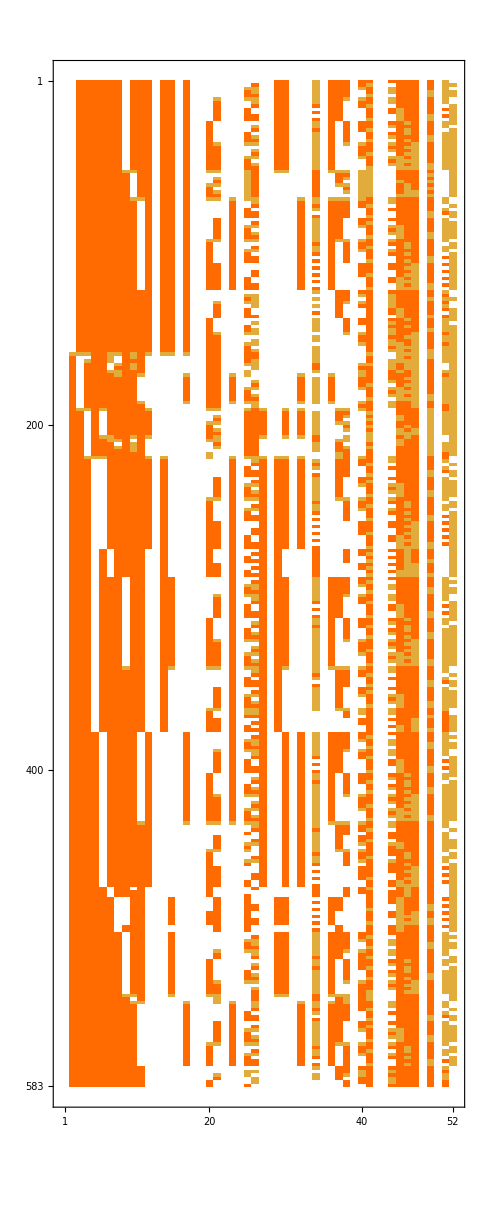

```mathematica
MatrixPlot[Sort[Map[BaseCoeff2[Total[ListofVars[#]],"C"]&,ExpressionToList[allCrit2]]],FrameTicks->{{All,All},{All,Flatten[With[{all=Bases["C","Variables"]},Table[Position[all,allGraphs5[k,"colofour"]],{k,alfa1s}]]]}},
FrameTicksStyle->{{Blue,Blue},{Blue,Blue}}]
```

```mathematica
Intersection[ExpressionToList[allCrit],ExpressionToList[allCrit2]]
```

{}

```mathematica
ExpressionToList[allCrit]
```

{v124x35>0&&v12x3x4x5>0&&v134x25>0&&v135x24>0&&v13x245>0&&v13x24x5>0&&v13x25x4>0&&v14x235>0&&v14x25x3>0&&v14x2x35>0&&v15x2x3x4>0&&v1x23x4x5>0&&v1x24x35>0&&v1x2x34x5>0&&v1x2x3x45>0,v124x35>0&&v12x3x4x5>0&&v134x25>0&&v135x24>0&&v13x245>0&&v13x24x5>0&&v13x25x4>0&&v14x235>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x23x4x5>0&&v1x2x34x5>0&&v1x2x35x4>0&&v1x2x3x45>0,540,v124x3x5>0&&v12x35x4>0&&v134x2x5>0&&v135x2x4>0&&v13x2x45>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x24x3>0&&v1x235x4>0&&v1x245x3>0&&v1x24x35>0&&v1x25x34>0&&v1x25x3x4>0,v124x3x5>0&&v12x35x4>0&&v134x2x5>0&&v135x2x4>0&&v13x2x45>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x24x3>0&&v1x235x4>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0}
 |  |  |  |

```mathematica
ExpressionToList[allCrit2]
```

{v12345>1&&v1234x5>1&&v1235x4>1&&v123x4x5>1&&v1245x3>1&&v125x3x4>1&&v12x34x5>1&&v12x3x45>1&&v134x25>1&&v135x24>1&&v13x245>1&&v13x2x4x5>0&&v145x2x3>1&&v14x235>1&&v14x2x35>1&&v14x2x3x5>0&&v15x2x3x4>1&&v1x23x45>1&&v1x23x4x5>1&&v1x24x35>1&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x345>1&&v1x2x34x5>1&&v1x2x35x4>0,581,v124x35>1&&v12x3x4x5>1&&v134x25>1&&v135x24>1&&v13x245>1&&v13x24x5>1&&v13x25x4>1&&v14x235>1&&v14x25x3>1&&v14x2x35>1&&v15x2x3x4>1&&v1x23x4x5>1&&v1x24x35>1&&v1x2x34x5>1&&v1x2x3x45>1}
 |  |  |  |

```mathematica
Length[allCrit]
```

544

```mathematica
Length[allCrit2]
```

583

```mathematica
allCrit2[[1]]
```

v12345>1&&v1234x5>1&&v1235x4>1&&v123x4x5>1&&v1245x3>1&&v125x3x4>1&&v12x34x5>1&&v12x3x45>1&&v134x25>1&&v135x24>1&&v13x245>1&&v13x2x4x5>0&&v145x2x3>1&&v14x235>1&&v14x2x35>1&&v14x2x3x5>0&&v15x2x3x4>1&&v1x23x45>1&&v1x23x4x5>1&&v1x24x35>1&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x345>1&&v1x2x34x5>1&&v1x2x35x4>0

```mathematica
Table[allGraphs5[k,"comp"]=Greater;allGraphs5[k,"compwhy"]=ToString[allCrit2[[1]]];
allGraphs5[k,"atleast"]=2;allGraphs5[k,"atleastwhy"]=ToString[allCrit2[[1]]];k,{k,ListofVars[allCrit2[[1]]]/.RepKey["C"]}]
```

{59048,58288,56770,56011,52232,49963,49216,49208,38308,36898,36194,36085,32441,31984,31714,31711,30253,29768,29767,29608,29605,29551,29537,29533,29527}

```mathematica
{Sort[ListofVars[allCrit2[[1]]]],Sort[ListofVars[allCrit[[1]]]]}
```

{{v12345,v1234x5,v1235x4,v123x4x5,v1245x3,v125x3x4,v12x34x5,v12x3x45,v134x25,v135x24,v13x245,v13x2x4x5,v145x2x3,v14x235,v14x2x35,v14x2x3x5,v15x2x3x4,v1x23x45,v1x23x4x5,v1x24x35,v1x24x3x5,v1x25x3x4,v1x2x345,v1x2x34x5,v1x2x35x4},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v13x25x4,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x35,v1x2x34x5,v1x2x3x45}}

```mathematica
Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Table[ShowGraph5Least[k],{k,ListofVars[allCrit2[[1]]]/.RepKey["C"]}]
```

{-Graphics-590482,-Graphics-582882,-Graphics-567702,-Graphics-560112,-Graphics-522322,-Graphics-499632,-Graphics-492162,-Graphics-492082,-Graphics-383082,-Graphics-368982,-Graphics-361942,-Graphics-360852,-Graphics-324412,-Graphics-319842,-Graphics-317142,-Graphics-317112,-Graphics-302532,-Graphics-297682,-Graphics-297672,-Graphics-296082,-Graphics-296052,-Graphics-295512,-Graphics-295372,-Graphics-295332,-Graphics-295272}

```mathematica
Table[allGraphs5[k,"comp"],{k,allGraphs5AtomKeys}]//Tally
```

{{Equal,1},{Greater,41},{GreaterEqual,10}}

```mathematica
PropagateAtLeast2[]
```

{0,{}}

```mathematica
PropagateComp[]
```

0

```mathematica
allCrit3=With[
{base="C",colofour="colofour"},
Fold[And,
Map[Fold[Or,Table[var>(var/.RepAtLeast[base]),{var,ListofVars[(allGraphs5[#,colofour]/.RepZero[base])]}]]&,
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
]
]
];
```

```mathematica
Take[allCrit3,10]
```

(v12345>2||v1234x5>2||v1235x4>2||v123x45>1||v123x4x5>2||v1245x3>2||v124x35>1||v124x3x5>0||v125x34>1||v125x3x4>2||v12x345>1||v12x34x5>2||v12x35x4>0||v12x3x45>2||v12x3x4x5>1||v1345x2>1||v134x25>2||v134x2x5>0||v135x24>2||v135x2x4>0||v13x245>2||v13x24x5>1||v13x25x4>1||v13x2x45>0||v13x2x4x5>2||v145x23>1||v145x2x3>2||v14x235>2||v14x23x5>0||v14x25x3>1||v14x2x35>2||v14x2x3x5>2||v15x234>1||v15x23x4>1||v15x24x3>0||v15x2x34>1||v15x2x3x4>2||v1x2345>1||v1x234x5>1||v1x235x4>0||v1x23x45>2||v1x23x4x5>2||v1x245x3>0||v1x24x35>2||v1x24x3x5>2||v1x25x34>0||v1x25x3x4>2||v1x2x345>2||v1x2x34x5>2||v1x2x35x4>2||v1x2x3x45>1)&&(v1345x2>1||v134x25>2||v134x2x5>0||v135x24>2||v135x2x4>0||v13x245>2||v13x24x5>1||v13x25x4>1||v13x2x45>0||v13x2x4x5>2||v145x23>1||v145x2x3>2||v14x235>2||v14x23x5>0||v14x25x3>1||v14x2x35>2||v14x2x3x5>2||v15x234>1||v15x23x4>1||v15x24x3>0||v15x2x34>1||v15x2x3x4>2||v1x2345>1||v1x234x5>1||v1x235x4>0||v1x23x45>2||v1x23x4x5>2||v1x245x3>0||v1x24x35>2||v1x24x3x5>2||v1x25x34>0||v1x25x3x4>2||v1x2x345>2||v1x2x34x5>2||v1x2x35x4>2||v1x2x3x45>1)&&(v145x23>1||v145x2x3>2||v14x235>2||v14x23x5>0||v14x25x3>1||v14x2x35>2||v14x2x3x5>2||v15x234>1||v15x23x4>1||v15x24x3>0||v15x2x34>1||v15x2x3x4>2||v1x2345>1||v1x234x5>1||v1x235x4>0||v1x23x45>2||v1x23x4x5>2||v1x245x3>0||v1x24x35>2||v1x24x3x5>2||v1x25x34>0||v1x25x3x4>2||v1x2x345>2||v1x2x34x5>2||v1x2x35x4>2||v1x2x3x45>1)&&(v15x234>1||v15x23x4>1||v15x24x3>0||v15x2x34>1||v15x2x3x4>2||v1x2345>1||v1x234x5>1||v1x235x4>0||v1x23x45>2||v1x23x4x5>2||v1x245x3>0||v1x24x35>2||v1x24x3x5>2||v1x25x34>0||v1x25x3x4>2||v1x2x345>2||v1x2x34x5>2||v1x2x35x4>2||v1x2x3x45>1)&&(v1x2345>1||v1x234x5>1||v1x235x4>0||v1x23x45>2||v1x23x4x5>2||v1x245x3>0||v1x24x35>2||v1x24x3x5>2||v1x25x34>0||v1x25x3x4>2||v1x2x345>2||v1x2x34x5>2||v1x2x35x4>2||v1x2x3x45>1)&&(v1x245x3>0||v1x24x35>2||v1x24x3x5>2||v1x25x34>0||v1x25x3x4>2||v1x2x345>2||v1x2x34x5>2||v1x2x35x4>2||v1x2x3x45>1)&&(v1x25x34>0||v1x25x3x4>2||v1x2x345>2||v1x2x34x5>2||v1x2x35x4>2||v1x2x3x45>1)&&(v1x2x345>2||v1x2x34x5>2||v1x2x35x4>2||v1x2x3x45>1)&&(v1x2x35x4>2||v1x2x3x45>1)&&(v1x2x345>2||v1x2x34x5>2)

```mathematica
Length[allCrit3]
```

1443

```mathematica
allCrit3=Reduce[allCrit3];Length[allCrit3]
```

783

```mathematica
allCrit3=BooleanMinimize[allCrit3];Length[allCrit3]
```

783

```mathematica
Take[allCrit3,10]
```

Take::normal: Nonatomic expression expected at position 1 in Take[allCrit3,10].

Take[allCrit3,10]

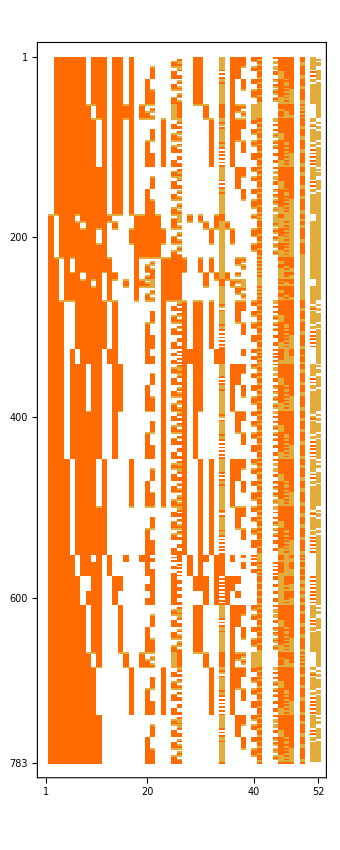

```mathematica
MatrixPlot[Sort[Map[BaseCoeff2[Total[ListofVars[#]],"C"]&,ExpressionToList[allCrit3]]],FrameTicks->{{All,All},{All,Flatten[With[{all=Bases["C","Variables"]},Table[Position[all,allGraphs5[k,"colofour"]],{k,alfa1s}]]]}},
FrameTicksStyle->{{Blue,Blue},{Blue,Blue}}]
```